Let’s examine the electrostatic vector field function.

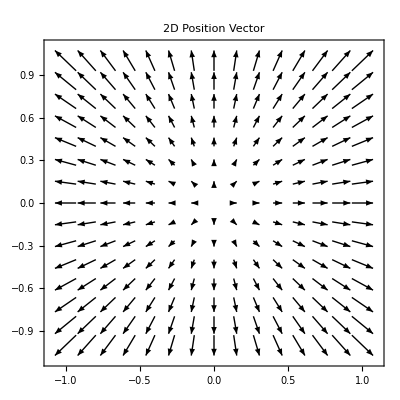

```mathematica
F[x_, y_] := UnitVector[2, 1]*x + 
    UnitVector[2, 2]*y; 
VectorPlot[F[i, j], {i, -1, 1}, 
  {j, -1, 1}, PlotLabel -> 
   "2D Position Vector"]
```

G[x_, y_] := (-ⅈy + ⅉx)/Sqrt[x^2 + y^2]

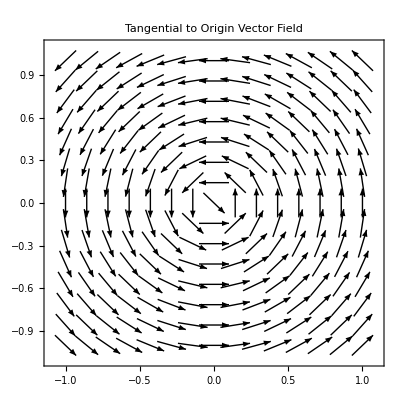

```mathematica
VectorPlot[G[i, j], {i, -1, 1}, 
  {j, -1, 1}, PlotLabel -> 
   "Tangential to Origin Vector Field"]
```

Now let’s look at the charge between two particles in free space in MKS units.  This law of Physics was discovered by the French physicist Charles-Augustin de Coulomb (June 1736 – 23 August 1806).  He was best known for developing Coulomb’s law, the definition of the electrostatic force of attraction and repulsion, but also did important work on friction. The SI unit of electric charge, the coulomb, was named after him.

```mathematica
CloudDeploy[
forceCoulombs[q1_,q2_,r_] := QuantityMagnitude[((q1*q2)/(4 π freeSpacePermitivity r^2))] Coulombs;
Manipulate[
r=Sqrt[(r1[[1]]-r2[[1]])^2 +(r1[[2]]-r2[[2]])^2];
Grid[
{{Text["Coulombs Law"]},
{Show[
ContourPlot[ϕ[q1,q2,r1[[1]],r1[[2]],r2[[1]],r2[[2]],x,y],{x,-2,2},{y,-1.5,1.5},Contours->10,ContourShading->False,
Epilog->{
Inset[Graphics[Text[Style[Subscript[Style["q",Italic],1],24,Black]]],{r1[[1]],r1[[2]]-.2}],Inset[Graphics[Text[Style[Subscript[Style["q",Italic],2],24,Black]]],{r2[[1]],r2[[2]]-.2}]}
],
ContourPlot[ψ[q1,q2,r1[[1]],r1[[2]],r2[[1]],r2[[2]],x,y],{x,-2,2},{y,-1.5,1.5},Contours->12,ContourStyle->Red,ContourShading->False],AspectRatio->2/3,ImageSize->{575,350}]
},{InputField[forceCoulombs[q1, q2,r],
FieldHint->"Coulombs",
FieldSize->20,
Enabled->False]}
}],
{{q1,1,"Charge " Subscript[q,1]},-2,2,.1,Appearance->"Labeled"},{{q2,-1,"Charge " Subscript[q,2]},-2,2,.1,Appearance->"Labeled"},{{r1,{-1,0}},{-2,-1.5},{2,1.5},Locator},
{{r2,{1,0}},{-2,-1.5},{2,1.5},Locator},
TrackedSymbols:>{q1,q2,r1,r2},Initialization:>(ϕ[q1_,q2_,x1_,y1_,x2_,y2_,x_,y_]:=q1/(√((x-x1)^2+(y-y1)^2)+.0001)+q2/(√((x-x2)^2+(y-y2)^2)+.0001);ψ[q1_,q2_,x1_,y1_,x2_,y2_,x_,y_]:=(q1 √((x-x2)^2+(y-y2)^2) (-(x-x1) (x1-x2)-(y-y1) (y1-y2))-q2 √((x-x1)^2+(y-y1)^2) ((x-x2) (x1-x2)+(y-y2) (y1-y2)))/(√((x-x1)^2+(y-y1)^2) √((x-x2)^2+(y-y2)^2) √((x1-x2)^2+(y1-y2)^2)+.0001))],Permissions->"Public"]
```

CloudObject[]

```mathematica
SetOptions[CloudObject["https://www.wolframcloud.com/objects/da99b6ea-9c81-4723-adb9-831a993984c5"],Permissions->"Public"]
```

{Permissions→Public}

Due the principle of superposition electrostatic charges add vectorially.  The electrostatic  field is the force per unit charge.  This is given by the following equation:

E(r)=(F(r))/q_0=1/(4 πϵ_0)q/r^2 û

This generalizes to:

E(r)=1/(4 πϵ_0)∑_(l=1)^n q_l/(|r-r_l|)^2(û)_l

Where (û)_l is the unit vector pointing from r_l to r and

r=𝕚x+𝕛y+𝕜z

produced by the charges q_1, q_2, ..., q_n

This just means the electrostatic field at r is the vector sum of the charges.  Electromagnetism is a field theory and will play a part in our derivation of Maxwell’s equation in a future blog post.

It is often convenient to treat the electrostatic charge as if it were continuous.  Suppose we have a volume of space denoted by ΔV with a charge in this space of ΔQ.  Then we define the average charge density in  ΔV as

(ρ̄)_ΔV≡ΔQ/ΔV

We now shrink the region around x, y, z by taking the limit.

ρ(x,y,z)≡(ΔV→^lim 0)_(about x,y,z)ΔQ/ΔV≡(ΔV→^lim 0)_(about x,y,z)(ρ̄)_ΔV

This allows us to express the electric charge in some region V as the following triple integral:

Q=∫∫∫_V ρ(x,y,z)dV

So for a continuos distribution of charges we may write:

E(r)=1/(4 πϵ_0)∫∫∫_V (ρ(r')û(r'))/(|r-r'|)^2 dV

Exercises I-1

(a)

```mathematica
f=ⅈx+ⅉy
```

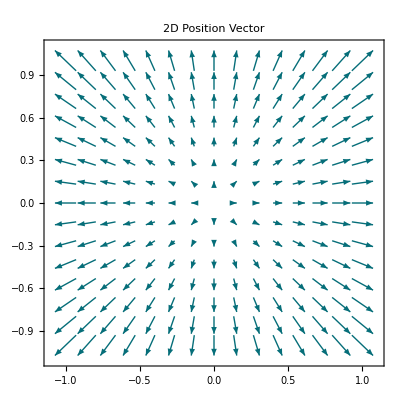

```mathematica
Fa[x_, y_] := UnitVector[2, 1]*x + 
    UnitVector[2, 2]*y; 
VectorPlot[Fa[i, j], {i, -1, 1}, 
  {j, -1, 1}, PlotLabel -> 
   "2D Position Vector"]
```

(b)

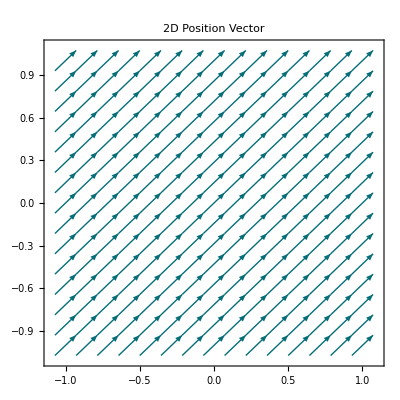

```mathematica
Fb[x_, y_] := (UnitVector[2, 1]+ 
    UnitVector[2, 2])/√2; 
VectorPlot[Fb[i, j], {i, -1, 1}, 
  {j, -1, 1}, PlotLabel -> 
   "2D Position Vector"]
```

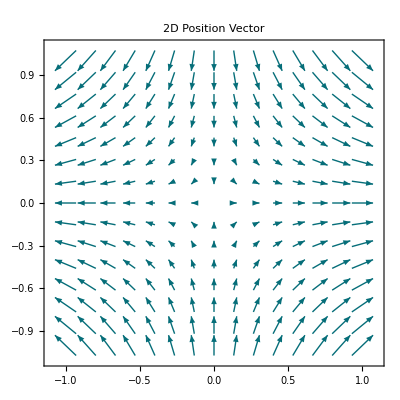

```mathematica
Fc[x_, y_] := UnitVector[2, 1]x- 
    UnitVector[2, 2]y; 
VectorPlot[Fc[i, j], {i, -1, 1}, 
  {j, -1, 1}, PlotLabel -> 
   "2D Position Vector"]
```

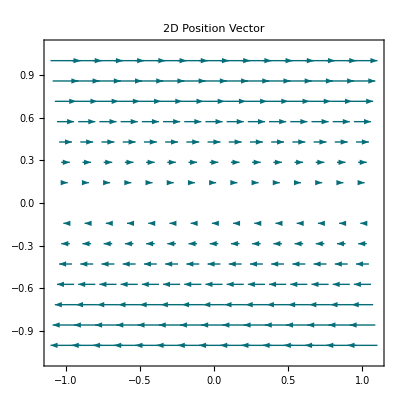

```mathematica
Fd[x_, y_] := UnitVector[2, 1]y; 
VectorPlot[Fd[i, j], {i, -1, 1}, 
  {j, -1, 1}, PlotLabel -> 
   "2D Position Vector"]
```

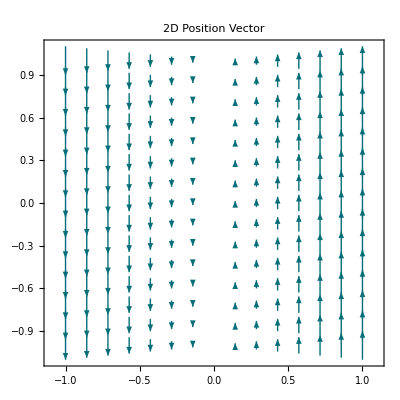

```mathematica
Fe[x_, y_] := UnitVector[2, 2]x; 
VectorPlot[Fe[i, j], {i, -1, 1}, 
  {j, -1, 1}, PlotLabel -> 
   "2D Position Vector"]
```

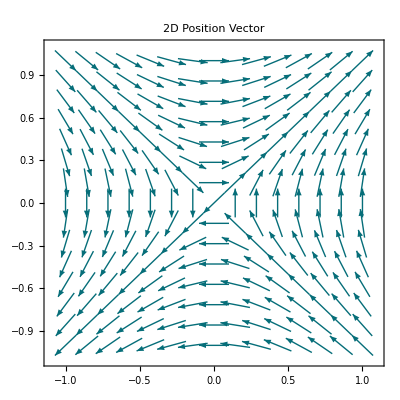

```mathematica
Ff[x_, y_] := (UnitVector[2, 1]y+UnitVector[2,2] x)/√(x^2+y^2); 
VectorPlot[Ff[i, j], {i, -1, 1}, 
  {j, -1, 1}, PlotLabel -> 
   "2D Position Vector"]
```

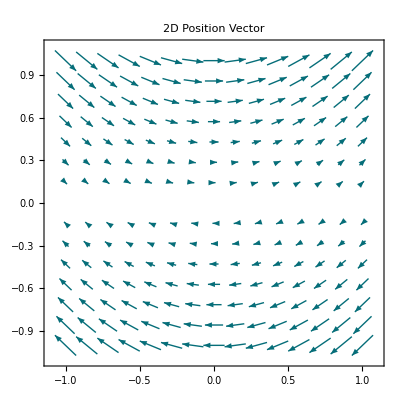

```mathematica
Fg[x_, y_] := UnitVector[2, 1]y+UnitVector[2,2] x y; 
VectorPlot[Fg[i, j], {i, -1, 1}, 
  {j, -1, 1}, PlotLabel -> 
   "2D Position Vector"]
```

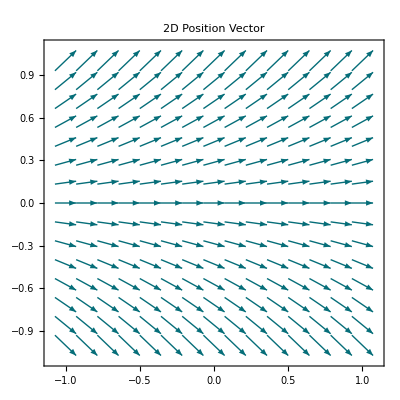

```mathematica
Fh[x_, y_] := UnitVector[2, 1]+UnitVector[2,2] y; 
VectorPlot[Fh[i, j], {i, -1, 1}, 
  {j, -1, 1}, PlotLabel -> 
   "2D Position Vector"]
```

Problem 1-2

The electric potential of a point charge is given by:

V=kQ/r=Q/(4 πϵ_0 r)

So that the radius r determines the potential.   The equipotential lines are therefor circles and a sphere centered on the charge is an equipotential surface. The dashed lines illustrate the scaling of voltage at equal increments - the equipotential lines get further apart with increasing r.

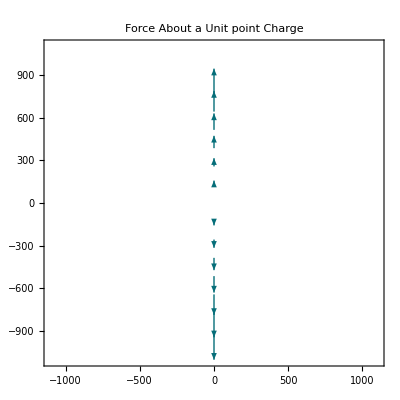

Set::write: Tag Times in 0.792778 kQ is Protected.

```mathematica
f3[x_,y_]:= (UnitVector[2, 1]x +UnitVector[2,2] y )/x^2+ y^2;
VectorPlot[f3[i, j], {i, -1000, 1000}, 
  {j,-1000, 1000}, PlotLabel ->  "Force About a Unit point Charge"]
```

```mathematica
VectorPlot3D[{x,y,z}/   Sqrt[x^2+y^2+z^2],{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

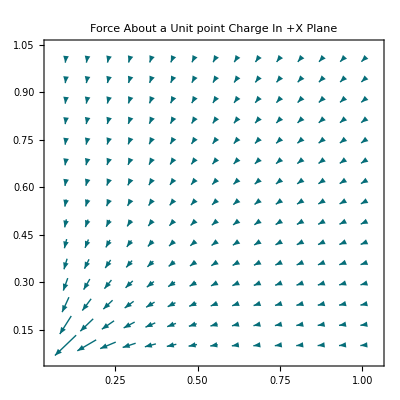

```mathematica
Subscript[k, e]=8.987551787; (* Coulombs constant *)
Q =-1;
Subscript[F, c][x_,y_,q_]=q Subscript[k, e](UnitVector[2, 1]x +UnitVector[2,2] y )/(x^2+y^2); VectorPlot[Subscript[F, c][i, j,Q], {i, 0.1, 1},   {j,0.1, 1}, PlotLabel ->  "Force About a Unit point Charge In +X Plane"]
```